## Tensors

The purpose of this notebook is to become acquainted with the Mathematica syntax for dealing with tensors and the tensorial math behind general relativity primarily, and physics in general.

#### packages

```mathematica
Get["MaTeX`"]
```

## Rank 0 Tensors

Rank 0 tensors are otherwise known as scalars. Scalars are just a number, and represent a magnitude only.

```mathematica
s=5; (* eg of an integer scalar*)
```

```mathematica
(*Rank 0 Tensors (Scalars)*)(*1. Defining scalars*)a=5;
b=3.14;
c=2+3I;(*Complex number*)Print["Scalar a = ",a]
Print["Scalar b = ",b]
Print["Scalar c = ",c]

(*2. Basic arithmetic operations*)
sum=a+b;
product=a*b;
quotient=a/b;
power=a^b;

Print["a + b = ",sum]
Print["a * b = ",product]
Print["a / b = ",quotient]
Print["a^b = ",power]

(*3. Mathematical functions*)
squareRoot=Sqrt[a];
exponential=Exp[b];
logarithm=Log[a];
absoluteValue=Abs[c];

Print["√a = ",squareRoot]
Print["e^b = ",exponential]
Print["ln(a) = ",logarithm]
Print["|c| = ",absoluteValue]

(*4. Trigonometric functions*)
angle=Pi/4;
sinValue=Sin[angle];
cosValue=Cos[angle];
tanValue=Tan[angle];

Print["sin(π/4) = ",sinValue]
Print["cos(π/4) = ",cosValue]
Print["tan(π/4) = ",tanValue]

(*5. Symbolic manipulation*)
Clear[x,y]
expr=x^2+2x+1;
expandedExpr=Expand[(x+1)^2];
factoredExpr=Factor[x^2+2x+1];

Print["Expression: ",expr]
Print["Expanded: ",expandedExpr]
Print["Factored: ",factoredExpr]

(*6. Solving equations*)
solution=Solve[x^2-5x+6==0,x];

Print["Solutions to x^2 - 5x + 6 = 0: ",solution]

(*7. Numerical approximations*)
piApprox=N[Pi,20];
eApprox=N[E,20];

Print["π ≈ ",piApprox]
Print["e ≈ ",eApprox]

(*8. Unit conversion (as scalar operation)*)
metersToFeet=UnitConvert[Quantity[1,"Meters"],"Feet"];

Print["1 meter = ",metersToFeet]

(*9. Plotting a scalar field in 2D*)
scalarFieldPlot=Plot3D[Sin[x]*Cos[y],{x,-3,3},{y,-3,3},PlotLabel->"Scalar Field: f(x,y) = sin(x) * cos(y)",AxesLabel->{"x","y","z"}]
```

Scalar a = 5

Scalar b = 3.14

Scalar c = 2+3 ⅈ

a + b = 8.14

a * b = 15.7

a / b = 1.59236

a^b = 156.591

√a = √5

e^b = 23.1039

ln(a) = Log[5]

|c| = √13

sin(π/4) = 1/(√2)

cos(π/4) = 1/(√2)

tan(π/4) = 1

Expression: 1+2 x+x^2

Expanded: 1+2 x+x^2

Factored: (1+x)^2

Solutions to x^2 - 5x + 6 = 0: {{x→2},{x→3}}

π ≈ 3.1415926535897932385

e ≈ 2.7182818284590452354

1 meter = 1250/381 ft

-Graphics3D-

## Rank 1 Tensors

v1 = {1,2,3}

v2 = {4,5,6}

Symbolic vector = {x,y,z}

v1 + v2 = {5,7,9}

v1 - v2 = {-3,-3,-3}

2 * v1 = {2,4,6}

v1 / 2 = {1/2,1,3/2}

v1 · v2 = 32

Symbolic dot product = 5 x+3.14 y+(2+3 ⅈ) z

v1 × v2 = {-3,6,-3}

Symbolic cross product = {(2+3 ⅈ) y-3.14 z,(-2-3 ⅈ) x+5 z,3.14 x-5 y}

||v1|| = √14

Symbolic magnitude = √(Abs[x]^2+Abs[y]^2+Abs[z]^2)

Unit vector of v1 = {1/(√14),√(2/7),3/(√14)}

Angle between v1 and v2 (in radians) = ArcCos[(16 √(2/11))/7]

Angle between v1 and v2 (in degrees) = 12.9332

Projection of v1 onto v2 = {128/77,160/77,192/77}

Determinant of vectors = 0

Vectors are linearly independent: False

Transformation matrix from basis A to B = (Cos[θ]/(Cos[θ]^2+Sin[θ]^2) | Sin[θ]/(Cos[θ]^2+Sin[θ]^2)
-Sin[θ]/(Cos[θ]^2+Sin[θ]^2) | Cos[θ]/(Cos[θ]^2+Sin[θ]^2))

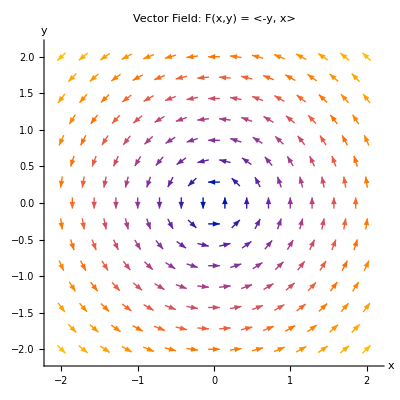

```mathematica
(*Rank 1 Tensors (Vectors)*)(*1. Defining vectors*)v1={1,2,3};
v2={4,5,6};
symbolicVector={x,y,z};

Print["v1 = ",v1]
Print["v2 = ",v2]
Print["Symbolic vector = ",symbolicVector]

(*2. Vector addition and subtraction*)
vectorSum=v1+v2;
vectorDiff=v1-v2;

Print["v1 + v2 = ",vectorSum]
Print["v1 - v2 = ",vectorDiff]

(*3. Scalar multiplication and division*)
scalar=2;
scaledVector=scalar*v1;
dividedVector=v1/scalar;

Print[scalar," * v1 = ",scaledVector]
Print["v1 / ",scalar," = ",dividedVector]

(*4. Dot product*)
dotProduct=v1.v2;
symbolicDotProduct=symbolicVector.{a,b,c};

Print["v1 · v2 = ",dotProduct]
Print["Symbolic dot product = ",symbolicDotProduct]

(*5. Cross product*)
crossProduct=Cross[v1,v2];
symbolicCrossProduct=Cross[symbolicVector,{a,b,c}];

Print["v1 × v2 = ",crossProduct]
Print["Symbolic cross product = ",symbolicCrossProduct]

(*6. Vector magnitude*)
magnitude=Norm[v1];
symbolicMagnitude=Simplify[Norm[symbolicVector]];

Print["||v1|| = ",magnitude]
Print["Symbolic magnitude = ",symbolicMagnitude]

(*7. Unit vector*)
unitVector=Normalize[v1];

Print["Unit vector of v1 = ",unitVector]

(*8. Angle between vectors*)
angle=VectorAngle[v1,v2];

Print["Angle between v1 and v2 (in radians) = ",angle]
Print["Angle between v1 and v2 (in degrees) = ",angle*180/Pi//N]

(*9. Vector projection*)
projection=(v1.v2/Norm[v2]^2)*v2;

Print["Projection of v1 onto v2 = ",projection]

(*10. Linear independence*)
vectors={{1,0,0},{0,1,0},{1,1,0}};
determinant=Det[vectors];

Print["Determinant of vectors = ",determinant]
Print["Vectors are linearly independent: ",determinant≠0]

(*11. Basis transformation*)
basisA={{1,0},{0,1}};
basisB={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
transformationMatrix=Inverse[basisB].basisA;

Print["Transformation matrix from basis A to B = ",transformationMatrix//MatrixForm]

(*12. Vector field visualization*)
vectorField=VectorPlot[{-y,x},{x,-2,2},{y,-2,2},VectorStyle->{Red,Arrowheads[0.03]},VectorPoints->15,VectorScale->{0.03,Automatic},Frame->False,Axes->True,AxesLabel->{"x","y"},PlotLabel->"Vector Field: F(x,y) = <-y, x>"]
```

## Rank 2 Tensors

m1 = (1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

m2 = (9 | 8 | 7
6 | 5 | 4
3 | 2 | 1)

Symbolic matrix = (5 | 3.14 | 2+3 ⅈ
d | e | f
g | h | i)

m1 + m2 = (10 | 10 | 10
10 | 10 | 10
10 | 10 | 10)

m1 - m2 = (-8 | -6 | -4
-2 | 0 | 2
4 | 6 | 8)

2 * m1 = (2 | 4 | 6
8 | 10 | 12
14 | 16 | 18)

m1 · m2 = (30 | 24 | 18
84 | 69 | 54
138 | 114 | 90)

Symbolic matrix product = (5 x+3.14 y+(2+3 ⅈ) z
d x+e y+f z
g x+h y+i z)

Transpose of m1 = (1 | 4 | 7
2 | 5 | 8
3 | 6 | 9)

Trace of m1 = 15

Determinant of m1 = 0

Inverse::sing: Matrix {{1,2,3},{4,5,6},{7,8,9}} is singular.

Inverse of m1 = Inverse[{{1,2,3},{4,5,6},{7,8,9}}]

Eigenvalues of m1 = {3/2 (5+√33),-3/2 (-5+√33),0}

Eigenvectors of m1 = (-(-15-√33)/(33+7 √33) | -(15-√33)/(-33+7 √33) | 1
(4 (6+√33))/(33+7 √33) | (4 (-6+√33))/(-33+7 √33) | -2
1 | 1 | 1)

exp(m1) = (1/6-(5 ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(√(11/3) ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(5 ⅇ^(15/2+(3 √33)/2))/(33+5 √33)+(√(11/3) ⅇ^(15/2+(3 √33)/2))/(33+5 √33) | -1/3-(14 ⅇ^(15/2-(3 √33)/2))/(3 (-33+5 √33))+(2 √(11/3) ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(14 ⅇ^(15/2+(3 √33)/2))/(3 (33+5 √33))+(2 √(11/3) ⅇ^(15/2+(3 √33)/2))/(33+5 √33) | 1/6-(13 ⅇ^(15/2-(3 √33)/2))/(3 (-33+5 √33))+(√33 ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(13 ⅇ^(15/2+(3 √33)/2))/(3 (33+5 √33))+(√33 ⅇ^(15/2+(3 √33)/2))/(33+5 √33)
-1/3-(8 ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(4 √(11/3) ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(8 ⅇ^(15/2+(3 √33)/2))/(33+5 √33)+(4 √(11/3) ⅇ^(15/2+(3 √33)/2))/(33+5 √33) | 2/3-(29 ⅇ^(15/2-(3 √33)/2))/(3 (-33+5 √33))+(5 √(11/3) ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(29 ⅇ^(15/2+(3 √33)/2))/(3 (33+5 √33))+(5 √(11/3) ⅇ^(15/2+(3 √33)/2))/(33+5 √33) | -1/3-(34 ⅇ^(15/2-(3 √33)/2))/(3 (-33+5 √33))+(2 √33 ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(34 ⅇ^(15/2+(3 √33)/2))/(3 (33+5 √33))+(2 √33 ⅇ^(15/2+(3 √33)/2))/(33+5 √33)
1/6-(11 ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(7 √(11/3) ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(11 ⅇ^(15/2+(3 √33)/2))/(33+5 √33)+(7 √(11/3) ⅇ^(15/2+(3 √33)/2))/(33+5 √33) | -1/3-(44 ⅇ^(15/2-(3 √33)/2))/(3 (-33+5 √33))+(8 √(11/3) ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(44 ⅇ^(15/2+(3 √33)/2))/(3 (33+5 √33))+(8 √(11/3) ⅇ^(15/2+(3 √33)/2))/(33+5 √33) | 1/6-(55 ⅇ^(15/2-(3 √33)/2))/(3 (-33+5 √33))+(3 √33 ⅇ^(15/2-(3 √33)/2))/(-33+5 √33)+(55 ⅇ^(15/2+(3 √33)/2))/(3 (33+5 √33))+(3 √33 ⅇ^(15/2+(3 √33)/2))/(33+5 √33))

Kronecker product of m1 and m2 = (9 | 8 | 7 | 18 | 16 | 14 | 27 | 24 | 21
6 | 5 | 4 | 12 | 10 | 8 | 18 | 15 | 12
3 | 2 | 1 | 6 | 4 | 2 | 9 | 6 | 3
36 | 32 | 28 | 45 | 40 | 35 | 54 | 48 | 42
24 | 20 | 16 | 30 | 25 | 20 | 36 | 30 | 24
12 | 8 | 4 | 15 | 10 | 5 | 18 | 12 | 6
63 | 56 | 49 | 72 | 64 | 56 | 81 | 72 | 63
42 | 35 | 28 | 48 | 40 | 32 | 54 | 45 | 36
21 | 14 | 7 | 24 | 16 | 8 | 27 | 18 | 9)

Symmetric part of m1 = (1 | 3 | 5
3 | 5 | 7
5 | 7 | 9)

Antisymmetric part of m1 = (0 | -1 | -2
1 | 0 | -1
2 | 1 | 0)

Tensor product of v1 and v2 = (4 | 5 | 6
8 | 10 | 12
12 | 15 | 18)

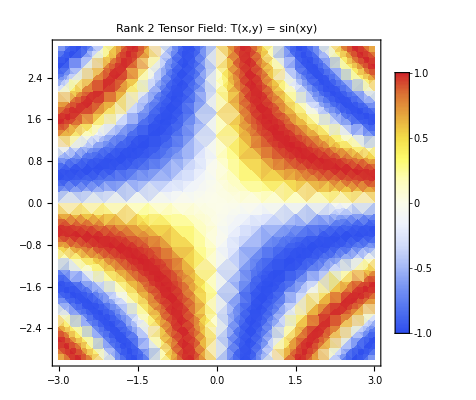

```mathematica
(*Rank 2 Tensors (Matrices)*)(*1. Defining matrices*)m1={{1,2,3},{4,5,6},{7,8,9}};
m2={{9,8,7},{6,5,4},{3,2,1}};
symbolicMatrix={{a,b,c},{d,e,f},{g,h,i}};

Print["m1 = ",MatrixForm[m1]]
Print["m2 = ",MatrixForm[m2]]
Print["Symbolic matrix = ",MatrixForm[symbolicMatrix]]

(*2. Matrix addition and subtraction*)
matrixSum=m1+m2;
matrixDiff=m1-m2;

Print["m1 + m2 = ",MatrixForm[matrixSum]]
Print["m1 - m2 = ",MatrixForm[matrixDiff]]

(*3. Scalar multiplication*)
scalar=2;
scaledMatrix=scalar*m1;

Print[scalar," * m1 = ",MatrixForm[scaledMatrix]]

(*4. Matrix multiplication*)
matrixProduct=m1.m2;
symbolicProduct=symbolicMatrix.{{x},{y},{z}};

Print["m1 · m2 = ",MatrixForm[matrixProduct]]
Print["Symbolic matrix product = ",MatrixForm[symbolicProduct]]

(*5. Transpose*)
transposed=Transpose[m1];

Print["Transpose of m1 = ",MatrixForm[transposed]]

(*6. Trace*)
trace=Tr[m1];

Print["Trace of m1 = ",trace]

(*7. Determinant*)
det=Det[m1];

Print["Determinant of m1 = ",det]

(*8. Inverse*)
inverse=Inverse[m1];

Print["Inverse of m1 = ",MatrixForm[inverse]]

(*9. Eigenvalues and Eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[m1];

Print["Eigenvalues of m1 = ",eigenvalues]
Print["Eigenvectors of m1 = ",MatrixForm[Transpose[eigenvectors]]]

(*10. Matrix exponential*)
expM=MatrixExp[m1];

Print["exp(m1) = ",MatrixForm[expM]]

(*11. Kronecker product*)
kroneckerProduct=KroneckerProduct[m1,m2];

Print["Kronecker product of m1 and m2 = ",MatrixForm[kroneckerProduct]]

(*12. Symmetric and antisymmetric parts*)
symmetricPart=(m1+Transpose[m1])/2;
antisymmetricPart=(m1-Transpose[m1])/2;

Print["Symmetric part of m1 = ",MatrixForm[symmetricPart]]
Print["Antisymmetric part of m1 = ",MatrixForm[antisymmetricPart]]

(*13. Tensor product of vectors*)
v1={1,2,3};
v2={4,5,6};
tensorProduct=TensorProduct[v1,v2];

Print["Tensor product of v1 and v2 = ",MatrixForm[tensorProduct]]

(*14. Visualizing a rank 2 tensor field*)
tensorFieldPlot=DensityPlot[Sin[x y],{x,-3,3},{y,-3,3},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotLabel->"Rank 2 Tensor Field: T(x,y) = sin(xy)"]
```

## Tensor Contraction

```mathematica
(*Tensor Contraction Example*)(*1. Define a rank 3 tensor*)t={{{1,2,3},{4,5,6},{7,8,9}},{{10,11,12},{13,14,15},{16,17,18}},{{19,20,21},{22,23,24},{25,26,27}}};

Print["Original rank 3 tensor t:"]
Print[MatrixForm[#]&/@t]

(*2. Single contraction (over first and second indices)*)
singleContraction=TensorContract[t,{{1,2}}];

Print["\nSingle contraction (over first and second indices):"]
Print["Result (a vector):"]
Print[singleContraction]

(*Explanation of single contraction*)
Print["\nExplanation of single contraction:"]
Print["t[i,i,k] = ",ToString@Total[Table[t[[i,i,k]],{i,1,3},{k,1,3}],2]]
```

Original rank 3 tensor t:

{(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),(10 | 11 | 12
13 | 14 | 15
16 | 17 | 18),(19 | 20 | 21
22 | 23 | 24
25 | 26 | 27)}

Single contraction (over first and second indices):

Result (a vector):

{39,42,45}

Explanation of single contraction:

t[i,i,k] = 126

## Playing with Vectors and Tensors

```mathematica
(* Vectors *)
```

```mathematica
V= {1,2,3};
U={2,3,6};
```

```mathematica
W = U+V
```

{3,5,9}

```mathematica
VectorQ[W]
```

True

```mathematica
(* Create a function *)
```

```mathematica
f[x_]:=x^2;
```

```mathematica
(* Create a vector from the function f *)
```

```mathematica
Vf=Array[f, 3]
```

{1,4,9}

```mathematica
Length[Vf]
```

3

```mathematica
Set[Vf[[1]],2];
```

```mathematica
Vf
```

{2,4,9}

```mathematica
(* OR *)
```

```mathematica
Vf[[2]]=2;
```

```mathematica
Vf
```

{2,2,9}

```mathematica
(* Dot Product *)
```

```mathematica
V.W
```

40

```mathematica
(* Cross Product *)
```

```mathematica
Cross[V,W]
```

{3,0,-1}

```mathematica
(* Tensor Product *)
```

```mathematica
V⊗W
```

{{3,5,9},{6,10,18},{9,15,27}}

```mathematica
(* Kroneker Prodcut *)
```

```mathematica
KroneckerProduct[V,W]
```

{{3,5,9},{6,10,18},{9,15,27}}

```mathematica
Normal[LeviCivitaTensor[3]]//MatrixForm
```

((0
0
0) | (0
0
1) | (0
-1
0)
(0
0
-1) | (0
0
0) | (1
0
0)
(0
1
0) | (-1
0
0) | (0
0
0))

```mathematica
Norm[V]
```

√14

```mathematica
Normalize[V]
```

{1/(√14),√(2/7),3/(√14)}

```mathematica
T=V⊗W
```

{{3,5,9},{6,10,18},{9,15,27}}

```mathematica
VectorQ[T]
```

False

```mathematica
TensorQ[T]
```

True

```mathematica
ArrayQ[T]
```

True

```mathematica
Length[T]
```

3

```mathematica
Dimensions[T]
```

{3,3}

## Intro to Tensors NASA

```mathematica
ClearAll["Global`*"]
```

```mathematica
V={1,2,3};
U={2,4,6};
```

```mathematica
W=V+U;
```

```mathematica
V⊗U⊗W
```

{{{6,12,18},{12,24,36},{18,36,54}},{{12,24,36},{24,48,72},{36,72,108}},{{18,36,54},{36,72,108},{54,108,162}}}